## Minimization test

### Constants

```mathematica
a=3.4;
b=1-a;
th=0.2;
phi=1.2;
c0=2.4;
```

### Model function

```mathematica
f[x_,y_]:=a*(x^2 Sin[th]-c0)+b(y^2 Cos[th]Sin[phi]-c0)-x y;
```

```mathematica
contour[function_]:=ContourPlot[function[x,y],{x,-1,1},{y,-1,1}];
```

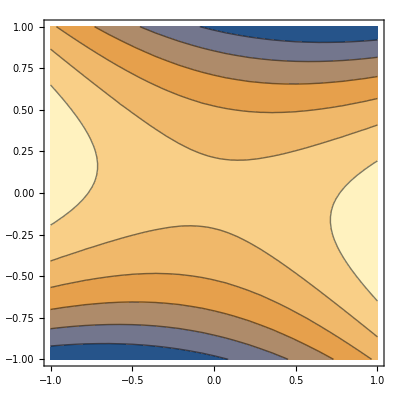

```mathematica
contour[f]
```